```mathematica
phi[n0_,n1_,n2_,n3_,n1v_,n2v_,nt1_,nt2_]:=-n0*Log[1-n3] + (n1*n2-n1v*n2v)/(1-n3) +((a+b)*n2^3-3*a*n2*n2v^2+3*a*n2v^2*nt2-3*b*n2*(2*nt1^2+nt2^2)+(2*b-a)*(2*nt1^3+nt2^3))*(n3+(1-n3)^2*Log[1-n3])/(36*Pi*n3^2*(1-n3)^2)
f =η*Log[η]+Pi/6*σ^3*phi[n0,n1,n2,n3,n1v,n2v,nt1,nt2]/.{n0->6*η/(π*σ^3),n1->3*η/(π*σ^2),n2->6*η/σ,n3->η,n1v->0,n2v->0,nt1->2*η/σ,nt2->2*η/σ}//Simplify
```

1/9 η (((27+8 a+2 b-27 η) η)/(-1+η)^2+(-9+8 a+2 b) Log[1-η]+9 Log[η])

```mathematica
p = -f + η*D[f,η]//Simplify;
mu = D[f-η*Log[η],η]//Simplify;
muCS=mu/.{a->3/2,b->-3/2}//Simplify;
mu-muCS//Simplify
z =Pi/6*σ^3*D[phi[n0,n1,n2,n3,n1v,n2v,nt1,nt2],n3]/.{n0->6*η/(π*σ^3),n1->3*η/(π*σ^2),n2->6*η/σ,n3->η,n1v->0,n2v->0,nt1->2*η/σ,nt2->2*η/σ}//Simplify ;
γ = Pi*σ^2*D[phi[n0,n1,n2,n3,n1v,n2v,nt1,nt2],n2]/.{n0->6*η/(π*σ^3),n1->3*η/(π*σ^2),n2->6*η/σ,n3->η,n1v->0,n2v->0,nt1->2*η/σ,nt2->2*η/σ}//Simplify;
χ = (η*D[mu+Log[η],η])^(-1)//Simplify
χCS =χ/.{a->3/2,b->-3/2}//Simplify
```

((-9+8 a+2 b) (η (-1-2 η+η^2)+(-1+η)^3 Log[1-η]))/(9 (-1+η)^3)

(9 (-1+η)^4)/(9+36 η+9 (-5+8 a+2 b) η^2-8 (4 a+b) η^3+2 (4 a+b) η^4)

(-1+η)^4/(1+4 η+4 η^2-4 η^3+η^4)

```mathematica
D[phi[n0,n1,n2,n3,n1v,n2v,nt1,nt2],n0]//Simplify
```

-Log[1-n3]

```mathematica
D[phi[n0,n1,n2,n3,n1v,n2v,nt1,nt2],n1]//Simplify
```

n2/(1-n3)

```mathematica
D[phi[n0,n1,n2,n3,n1v,n2v,nt1,nt2],n2]//Simplify
```

n1/(1-n3)+((a (n2^2-n2v^2)+b (n2^2-2 nt1^2-nt2^2)) (n3+(-1+n3)^2 Log[1-n3]))/(12 (-1+n3)^2 n3^2 π)

```mathematica
D[phi[n0,n1,n2,n3,n1v,n2v,nt1,nt2],n3]//Simplify
```

-1/(36 (-1+n3)^3 n3^3 π)(-36 (n1 n2-n1v n2v) (-1+n3) n3^3 π+36 n0 (-1+n3)^2 n3^3 π+(1-n3) n3 ((a+b) n2^3-3 a n2 n2v^2+3 a n2v^2 nt2-3 b n2 (2 nt1^2+nt2^2)-(a-2 b) (2 nt1^3+nt2^3)) (n3+2 (-1+n3) Log[1-n3])-2 (1-n3) ((a+b) n2^3-3 a n2 n2v^2+3 a n2v^2 nt2-3 b n2 (2 nt1^2+nt2^2)-(a-2 b) (2 nt1^3+nt2^3)) (n3+(-1+n3)^2 Log[1-n3])+2 n3 ((a+b) n2^3-3 a n2 n2v^2+3 a n2v^2 nt2-3 b n2 (2 nt1^2+nt2^2)-(a-2 b) (2 nt1^3+nt2^3)) (n3+(-1+n3)^2 Log[1-n3]))

```mathematica
D[phi[n0,n1,n2,n3,n1v,n2v,nt1,nt2],n1v]//Simplify
```

n2v/(-1+n3)

```mathematica
D[phi[n0,n1,n2,n3,n1v,n2v,nt1,nt2],n2v]//Simplify
```

(n3 (a n2v (-n2+nt2)+6 n1v (-1+n3) n3 π)-a n2v (-1+n3)^2 (n2-nt2) Log[1-n3])/(6 (-1+n3)^2 n3^2 π)

```mathematica
D[phi[n0,n1,n2,n3,n1v,n2v,nt1,nt2],nt1]//Simplify
```

-(nt1 (2 b (n2-nt1)+a nt1) (n3+(-1+n3)^2 Log[1-n3]))/(6 (-1+n3)^2 n3^2 π)

```mathematica
D[phi[n0,n1,n2,n3,n1v,n2v,nt1,nt2],nt2]//Simplify
```

((2 b nt2 (-n2+nt2)+a (n2v^2-nt2^2)) (n3+(-1+n3)^2 Log[1-n3]))/(12 (-1+n3)^2 n3^2 π)

```mathematica
pCS=η*(1+η+η^2-η^3)/(1-η)^3//Simplify
```

(η (1+η+η^2-η^3))/(1-η)^3

```mathematica
p-pCS//Simplify
```

((-9+8 a+2 b) (-3+η) η^3)/(9 (-1+η)^3)

```mathematica
p//Simplify
```

(η (-9-9 η-6 (-3+4 a+b) η^2+2 (4 a+b) η^3))/(9 (-1+η)^3)

```mathematica
mu-(η (-8+9 η-3 η^2))/(-1+η)^3//Simplify
```

((-9+8 a+2 b) (η (-1-2 η+η^2)+(-1+η)^3 Log[1-η]))/(9 (-1+η)^3)

```mathematica
p-z//Simplify
Series[p-z,{η,0,3}]//Simplify
```

(2 (4 a+b) ((-2+η) η+2 (-1+η) Log[1-η]))/(9 (-1+η))

2/27 (4 a+b) η^3+O[η]^4

```mathematica
pWB[η_,a_,b_]:=(η (-9-9 η-6 (-3+4 a+b) η^2+2 (4 a+b) η^3))/(9 (-1+η)^3)
```

```mathematica
zWB[η_,a_,b_]:=1/9 (η*(-9-9 η+18 η^2+8 a (2-5 η+η^2)+2 b (2-5 η+η^2))/(-1+η)^3-4 (4 a+b) Log[1-η])
```

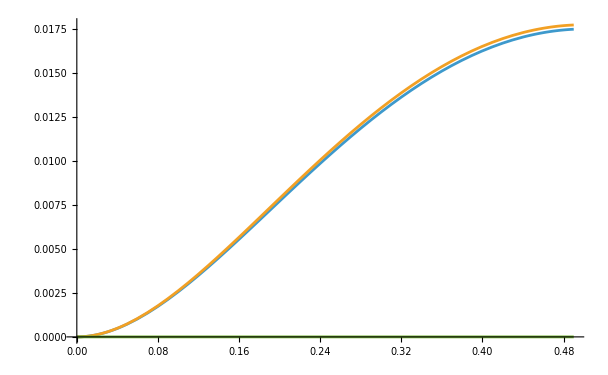

```mathematica
Plot[{(pWB[e,1.5,-1.5]-zWB[e,1.5,-1.5])/pWB[e,1.5,-1.5],(pWB[e,1.4,-1.]-zWB[e,1.4,-1.])/pWB[e,1.4,-1.],(pWB[e,1,-4]-zWB[e,1,-4])/pWB[e,1,-4]},{e,0.0,0.49}]
```